```mathematica
ClearAll["Global`*"]
<< HPL`;
```

ClearAll::wrsym: Symbol HPL is Protected.

ClearAll::wrsym: Symbol HPLMtoA is Protected.

Package HPL already loaded...

$Aborted

Extract equations (B.5) - (B.7) from [Vogt, Moch: “The third-order QCD corrections to deep-inelastic scattering by photon exchange” ,Nucl. Phys. B, 724 (1-2), 3, 2005] with the help of ChatGPT

```mathematica
pqq[x_]:=2/(1-x)-1-x;
pqg[x_]:=1-2 x+2 x^2;
pgq[x_]:=2/x-2+x;
pgg[x_]:=1/(1-x)+1/x-2+x-x^2;

c2ns2[x_]:=CF*(CF-CA/2)*((8/5)*(9*pqg[-x]*(1-x)+pgq[-x]*(1-x^-1)+(37+17*x))*HPL[{-1,0},x]+4*pqq[-x]*(7*Zeta3+6*HPL[{-2,0},x]+4*HPL[{-1,2},x]-8*HPL[{-1,-1,0},x]+10*HPL[{-1,0,0},x]-3*HPL[{0,0,0},x]-8*HPL[{-1},x]*Zeta2-2*HPL[{0},x]+2*HPL[{0},x]*Zeta2-2*HPL[{3},x])-(72/5)*pqg[x]*((1+x)*(Zeta2-HPL[{0,0},x])-1-HPL[{0},x])+(8/5)*pgq[x]*(1-HPL[{0},x])+8*(1-5*x)*(HPL[{1,0,0},x]-HPL[{1},x]*Zeta2)-8*(1+5*x)*(2*HPL[{-1,-1,0},x]-HPL[{-1,0,0},x]+HPL[{-1},x]*Zeta2))+CF*nf*(1/54*pqq[x]*(247-144*Zeta2+180*HPL[{0,0},x]+72*HPL[{1,0},x]+72*HPL[{1,1},x]+342*HPL[{0},x]+174*HPL[{1},x]+144*HPL[{2},x])-1/3*(7+19*x)*HPL[{0},x]-1/3*(1+13*x)*HPL[{1},x]-1/18*(23+243*x)+DiracDelta[1-x]*(457/36+4/3*Zeta3+38/3*Zeta2))+CF^2*(16*HPL[{-2,0},x]+1/5*(33+37*x)*HPL[{0,0},x]+1/4*pqq[x]*(51+128*Zeta3+48*Zeta2+96*HPL[{-2,0},x]-12*HPL[{0,0},x]-72*HPL[{1,0},x]-72*HPL[{1,1},x]-96*HPL[{1,2},x]-96*HPL[{2,0},x]-112*HPL[{2,1},x]-32*HPL[{0,0,0},x]-48*HPL[{1,0,0},x]-128*HPL[{1,1,0},x]-96*HPL[{1,1,1},x]+122*HPL[{0},x]+96*HPL[{0},x]*Zeta2+54*HPL[{1},x]+32*HPL[{1},x]*Zeta2-48*HPL[{2},x]-96*HPL[{3},x])-1/2*(43+63*x)*HPL[{0},x]+1/2*(59-109*x)*HPL[{1},x]-4*(1-19*x)*Zeta3+2*(1+x)*(7*HPL[{1,0},x]+2*HPL[{2,0},x]+2*HPL[{2,1},x]+5*HPL[{0,0,0},x]-4*HPL[{0},x]*Zeta2+4*HPL[{3},x])+2*(5+9*x)*(HPL[{1,1},x]+2*HPL[{2},x])-4/5*(7+13*x)*Zeta2-1/4*(93+209*x)+DiracDelta[1-x]*(331/8-78*Zeta3+69*Zeta2+6*Zeta2^2))+CA*CF*(-1/108*pqq[x]*(3155-216*Zeta3-1584*Zeta2+1296*HPL[{-2,0},x]+1980*HPL[{0,0},x]+792*HPL[{1,0},x]+792*HPL[{1,1},x]+432*HPL[{1,2},x]+648*HPL[{0,0,0},x]+864*HPL[{1,0,0},x]-432*HPL[{1,1,0},x]+4302*HPL[{0},x]-432*HPL[{0},x]*Zeta2+2202*HPL[{1},x]-1296*HPL[{1},x]*Zeta2+1584*HPL[{2},x]+432*HPL[{3},x])+1/6*(71+323*x)*HPL[{0},x]-17/6*(5-19*x)*HPL[{1},x]-4/5*(9+16*x)*(Zeta2-HPL[{0,0},x])+1/36*(139+3159*x)-8*(5*Zeta3*x+HPL[{-2,0},x])-DiracDelta[1-x]*(5465/72-140/3*Zeta3+251/3*Zeta2-71/5*Zeta2^2));

c2ps2[x_]:=Module[{},CF*(8/3*(-pqg[-x]+pgq[-x])*HPL[{-1,0},x]+8/27*pqg[x]*(28+27*Zeta2-36*HPL[{0,0},x]-9*HPL[{1,0},x]-9*HPL[{1,1},x]-24*HPL[{0},x]+6*HPL[{1},x]-27*HPL[{2},x])+4/27*pgq[x]*(43-18*Zeta2+18*HPL[{1,0},x]+18*HPL[{1,1},x]-39*HPL[{1},x])+8/9*(71-49*x)*HPL[{0},x]+4/3*(16-13*x)*HPL[{1},x]+8*(1-2*x)*HPL[{2},x]+12*(1-x)*(HPL[{1,0},x]+HPL[{1,1},x])-2/3*(1+x)*(12*Zeta3+12*HPL[{-1,0},x]-13*HPL[{0,0},x]-12*HPL[{2,0},x]-12*HPL[{2,1},x]-30*HPL[{0,0,0},x]+24*HPL[{0},x]*Zeta2-24*HPL[{3},x])+22/3*(3-5*x)-8/3*(5-x)*Zeta2)
];


c2g2[x_]:=Module[{},CF*((4/15)*(pgq[-x]*(1-x^-1)+(217+117*x))*HPL[{-1,0},x]+1/15*(639-1004*x)*HPL[{0,0},x]-(8/5)*pqg[-x]*(6*(1-x)*HPL[{-1,0},x]-5*(2*HPL[{-2,0},x]-2*HPL[{-1,-1,0},x]+HPL[{-1,0,0},x]-HPL[{-1},x]*Zeta2))+(2/5)*pqg[x]*(6*(19+4*x)*(Zeta2-HPL[{0,0},x])-(9-90*Zeta3+90*HPL[{1,0},x]+90*HPL[{1,1},x]+60*HPL[{1,2},x]+40*HPL[{2,0},x]+50*HPL[{2,1},x]+50*HPL[{0,0,0},x]+30*HPL[{1,0,0},x]+40*HPL[{1,1,0},x]+50*HPL[{1,1,1},x]+54*HPL[{0},x]-60*HPL[{0},x]*Zeta2+30*HPL[{1},x]-40*HPL[{1},x]*Zeta2+90*HPL[{2},x]+60*HPL[{3},x]))+(4/15)*pgq[x]*(1-HPL[{0},x])+1/3*(16-61*x)*HPL[{0},x]-2*(1-8*x)*HPL[{1},x]+4*(5-4*x)*HPL[{2},x]-4*(1-18*x)*Zeta3+2*(1-2*x)*(8*HPL[{-2,0},x]+2*HPL[{2,0},x]+2*HPL[{2,1},x]+5*HPL[{0,0,0},x]+4*HPL[{1,0,0},x]-4*HPL[{0},x]*Zeta2-4*HPL[{1},x]*Zeta2+4*HPL[{3},x])-8*(1+2*x)*(2*HPL[{-1,-1,0},x]-HPL[{-1,0,0},x]+HPL[{-1},x]*Zeta2)+2*(5+4*x)*(HPL[{1,0},x]+HPL[{1,1},x])-(4/15)*(111-176*x)*Zeta2-1/3*(117-121*x))+CA*((8/3)*(pgq[-x]-3*(4+3*x))*HPL[{-1,0},x]+(4/3)*HPL[{0,0},x]*(47+35*x)+2*(23-6*x)*HPL[{1,0},x]+6*(7-2*x)*HPL[{1,1},x]+4*(5+14*x)*HPL[{0,0,0},x]+(4/3)*pqg[-x]*(6*HPL[{-2,0},x]+10*HPL[{-1,0},x]+6*HPL[{-1,2},x]+9*HPL[{-1,0,0},x]-6*HPL[{-1},x]*Zeta2)-1/54*pqg[x]*(4493-648*Zeta3-3996*Zeta2+3492*HPL[{0,0},x]+2412*HPL[{1,0},x]+2196*HPL[{1,1},x]+216*HPL[{1,2},x]+432*HPL[{2,0},x]+432*HPL[{2,1},x]+432*HPL[{1,0,0},x]+648*HPL[{1,1,0},x]+216*HPL[{1,1,1},x]+6270*HPL[{0},x]-432*HPL[{0},x]*Zeta2+4710*HPL[{1},x]-216*HPL[{1},x]*Zeta2+3996*HPL[{2},x]+432*HPL[{3},x])+(4/27)*pgq[x]*(43-18*Zeta2+18*HPL[{1,0},x]+18*HPL[{1,1},x]-39*HPL[{1},x])+1/9*(1567-338*x)*HPL[{0},x]+1/3*(289-52*x)*HPL[{1},x]+2*(33-2*x)*HPL[{2},x]-4*(1-2*x)*(HPL[{1,0,0},x]-HPL[{1},x]*Zeta2)-4*(1+2*x)*(2*HPL[{-2,0},x]-2*HPL[{-1,-1,0},x]+HPL[{-1,0,0},x]-HPL[{-1},x]*Zeta2)-8*(1+3*x)*(Zeta3+2*HPL[{0},x]*Zeta2-2*HPL[{3},x])+8*(1+4*x)*(HPL[{2,0},x]+HPL[{2,1},x])+7/6*(105-46*x)-2/3*(107-10*x)*Zeta2)];
```

Compare to equations (4.8) - (4.10) from the same paper.

```mathematica
L0[x]:=Log[x];
L1[x]:=Log[1-x];
D0[x]:=1/(1-x);
D1[x]:=L1[x]/(1-x);
D2[x]:=L1[x]^2/(1-x);
D3[x]:=L1[x]^3/(1-x);

c2ns2appr[x_]=Module[{},
128/9*D3[x]-184/3*D2[x]-31.1052*D1[x]+188.641*D0[x]-338.513*DiracDelta[1-x]
-17.74*L1[x]^3+72.24*L1[x]^2-628.8*L1[x]-181.0-806.7*x+0.719*x*L0[x]^4
+L0[x]*L1[x]*(37.75*L0[x]-147.1*L1[x])-28.384*L0[x]-20.70*L0[x]^2-80/27*L0[x]^3
+nf*(
16/9*D2[x]-232/27*D1[x]+6.34888*D0[x]+46.8531*DiracDelta[1-x]-1.500*L1[x]^2
+24.87*L1[x]-7.8109-17.82*x-12.97*x^2-0.185*x*L0[x]^3+8.113*L0[x]*L1[x]
+16/3*L0[x]+20/9*L0[x]^2
)
];

c2ns2regappr[x_]=Module[{},
-17.74*L1[x]^3+72.24*L1[x]^2-628.8*L1[x]-181.0-806.7*x+0.719*x*L0[x]^4
+L0[x]*L1[x]*(37.75*L0[x]-147.1*L1[x])-28.384*L0[x]-20.70*L0[x]^2-80/27*L0[x]^3
+nf*(
-1.500*L1[x]^2
+24.87*L1[x]-7.8109-17.82*x-12.97*x^2-0.185*x*L0[x]^3+8.113*L0[x]*L1[x]
+16/3*L0[x]+20/9*L0[x]^2
)
];

c2ns2plusappr[x_]=Module[{},
128/9*D3[x]-184/3*D2[x]-31.1052*D1[x]+188.641*D0[x]
+nf*(
16/9*D2[x]-232/27*D1[x]+6.34888*D0[x]
)
];

c2ns2localappr[x_]=Module[{},
-338.513*DiracDelta[1-x]
+nf*(
46.8531*DiracDelta[1-x]
)
];

c2g2appr[x_]=Module[{},
58/9*L1[x]^3-24*L1[x]^2-34.88*L1[x]+30.586-(25.08+760.3*x
+29.65*L1[x]^3)*(1-x)+1204*x*L0[x]^2+L0[x]*L1[x]*(293.8+711.2*x+1043*L0[x])
+115.6*L0[x]-7.109*L0[x]^2+70/9*L0[x]^3+11.9033*(1-x)/x
];

c2ps2appr[x_]=Module[{},
(8/3*L1[x]^2-32/3*L1[x]+9.8937)*(1-x)+(9.57-13.41*x+0.08*L1[x]^3)*(1-x)^2
+5.667*x*L0[x]^3-L0[x]^2*L1[x]*(20.26-33.93*x)+43.36*(1-x)*L0[x]-1.053*L0[x]^2
+40/9*L0[x]^3+5.2903*(1-x)^2/x
];
```

The old parametrizations from [van Neerven, Vogt; Nucl. Phys. B. 568 (1-2), 263, 2000] eq. 3.2 and [van Neerven, Vogt; Nucl. Phys. B. 588 (1), 345, 2000] eq. 3.4, 3.6 is here...

```mathematica
c2ns2approld[x_]=Module[{},
14.2222* D3[x]−61.3333 *D2[x]−31.105 *D1[x]+188.64*D0[x]
−17.19 *L1[x]^3+71.08*L1[x]^2−660.7 *L1[x]+L1[x]*L0[x]*(−174.8 *L1[x]+95.09 *L0[x])
−2.835 *L0[x]^3−17.08 *L0[x]^2 +5.986 *L0[x]−1008* x−69.59−338.046 *DiracDelta[1−x]+
nf*(
1.77778 *D2[x]−8.5926 *D1[x]+6.3489*D0[x]
−1.707 *L1[x]^2+22.95 *L1[x]+L1[x]*L0[x](3.036 *L0[x]+17.97) 
+2.244 *L0[x]^2+5.770* L0[x]−37.91* x−5.691+46.8405 *DiracDelta[1-x]
)
];

c2ps2approld[x_]=Module[{},
-0.101*(1-x)*L1[x]^3-(24.75-13.80*x)*L1[x]*L0[x]^2+30.23*L1[x]*L0[x]
+4.310*L0[x]^3-2.086*L0[x]^2+39.78*L0[x]+5.290*(1/x-1)
];

c2g2approld[x_]=Module[{},
(6.445+209.4*(1-x))*L1[x]^3-24.00*L1[x]^2+(1494/x-1483)*L1[x]
+L1[x]*L0[x]*(-871.8*L1[x]-724.1*L0[x])+5.319*L0[x]^3-59.48*L0[x]^2-284.8*L0[x]
+11.90/x+392.4-0.28*DiracDelta[1-x]
];
```

First, check whether the parametrizations match

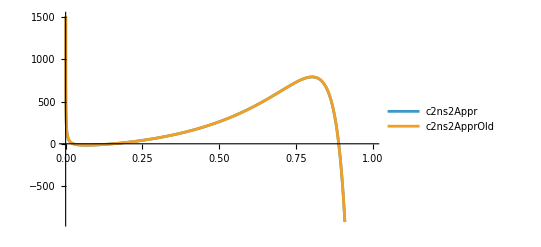

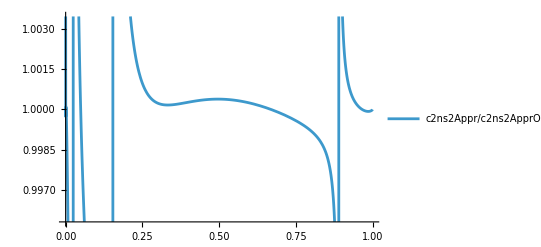

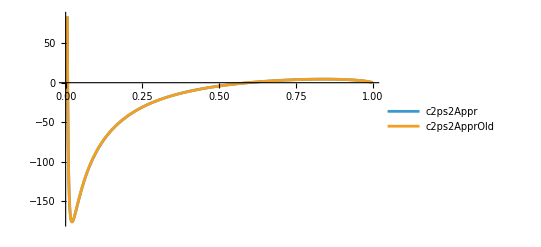

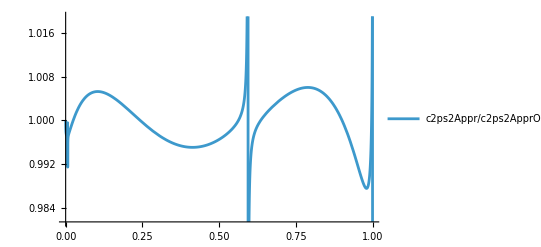

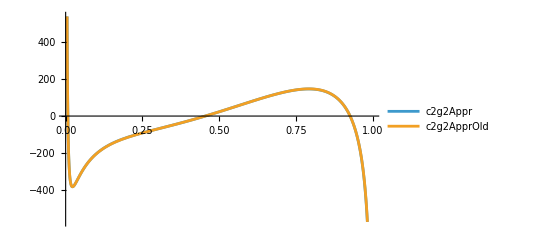

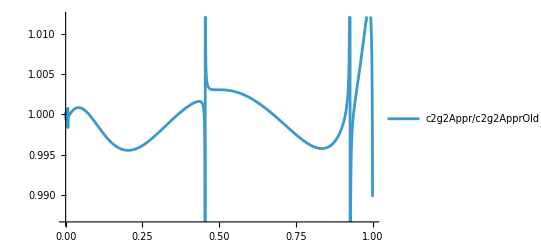

```mathematica
Plot[{
c2ns2appr[x]/.nf->3,
c2ns2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2ns2Appr","c2ns2ApprOld"}]
Plot[{
c2ns2appr[x]/c2ns2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2ns2Appr/c2ns2ApprOld"}]
Plot[{
c2ps2appr[x]/.nf->3,
c2ps2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2ps2Appr","c2ps2ApprOld"}]
Plot[{
c2ps2appr[x]/c2ps2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2ps2Appr/c2ps2ApprOld"}]
Plot[{
c2g2appr[x]/.nf->3,
c2g2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2g2Appr","c2g2ApprOld"}]
Plot[{
c2g2appr[x]/c2g2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2g2Appr/c2g2ApprOld"}]
```

If the parametrization coincide, then we are discussing the correct objects and there are probably no mismatches in notation etc. 

Now, let us check whether exact formula and (new) parametrization coincide...

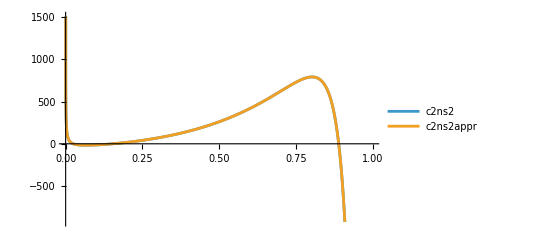

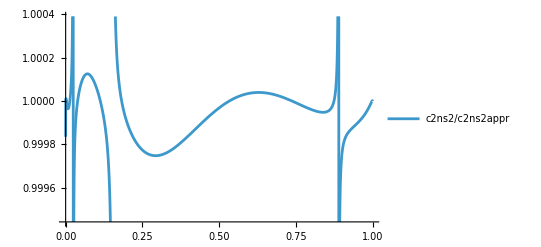

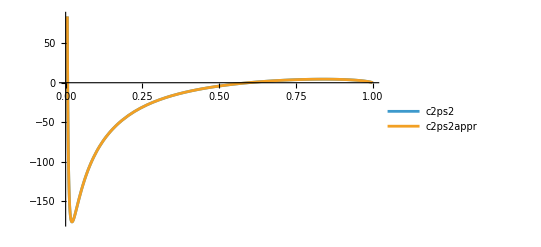

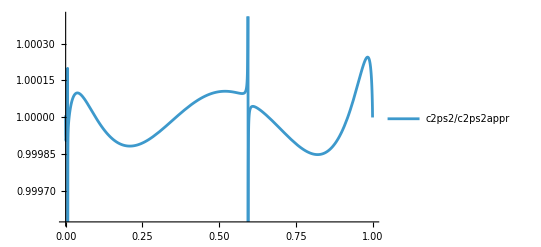

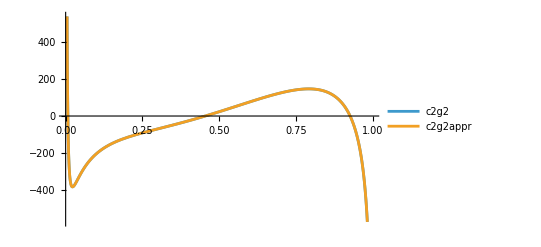

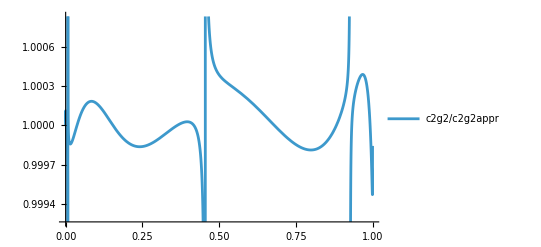

```mathematica
Plot[{
c2ns2[x]/.{nf->3,DiracDelta[x]->0,Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3},
c2ns2appr[x]/.{nf->3,DiracDelta[x]->0,Zeta2->Zeta[2],Zeta3->Zeta[3]}
},{x,0,1},PlotLegends->{"c2ns2","c2ns2appr"}]
Plot[
(c2ns2[x]/c2ns2appr[x])/.{nf->3,DiracDelta[x]->0,Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3}
,{x,0,1},PlotLegends->{"c2ns2/c2ns2appr"}]
Plot[{
c2ps2[x]/.{Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3},
c2ps2appr[x]/.{Zeta2->Zeta[2],Zeta3->Zeta[3]}
},{x,0,1},PlotLegends->{"c2ps2","c2ps2appr"}]
Plot[
(c2ps2[x]/c2ps2appr[x])/.{Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3}
,{x,0,1},PlotLegends->{"c2ps2/c2ps2appr"}]
Plot[{
c2g2[x]/.{Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3},
c2g2appr[x]/.{Zeta2->Zeta[2],Zeta3->Zeta[3]}
},{x,0,1},PlotLegends->{"c2g2","c2g2appr"}]
Plot[
(c2g2[x]/c2g2appr[x])/.{Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3}
,{x,0,1},PlotLegends->{"c2g2/c2g2appr"}]
```

This seems to match more or less.

Now let us rewrite the coefficient functions in a way that we can put into the C++ program.
We split the functions into Plus/Local/Regular part and format everything accordingly.

```mathematica
c2ns2x=c2ns2[x];

c2ns2xTerms=List@@Expand[c2ns2x];
c2ns2xlocalTerms=Select[c2ns2xTerms,!FreeQ[#,DiracDelta[1-x]]&];
c2ns2xplusTerms=Select[c2ns2xTerms,!FreeQ[#,1/(1-x)]&];
c2ns2xplusTermsHPL=Select[c2ns2xplusTerms,!FreeQ[#,HPL]&];
c2ns2xplusTermsNoHPL=Complement[c2ns2xplusTerms,c2ns2xplusTermsHPL];
c2ns2xregTerms=Complement[c2ns2xTerms,Join[c2ns2xlocalTerms,c2ns2xplusTerms]];

c2ns2xlocal=Total@c2ns2xlocalTerms//Collect[#,{DiracDelta[1-x],nf,CF,CA,Zeta2,Zeta3}]&;
c2ns2xplus=Total@c2ns2xplusTerms//Collect[#,{1/1(1-x),nf,CF,CA,Zeta2,Zeta3}]&;
c2ns2xreg=Total@c2ns2xregTerms//Collect[#,{nf,CF,CA,Zeta2,Zeta3}]&;

rHPL1=HPL[a_List,x_]:>myHPL[HPLMtoA[a],x];
rHPL2=myHPL[a_List,x_]:>With[{n=Length[a]},Symbol["HPL"<>ToString[n]][Sequence@@a,x]];
rHPLInt={
myHPL[a_List,x_]:>With[{n=Length[a]},Symbol["HPL"<>ToString[n+1]][1,Sequence@@a,x]],
1/(1-x)->1
};
rNoHPLInt=1/(1-x)->HPL[{1},x];(*-Log[1-x]*)

c2ns2xlocalplus=-Total@(c2ns2xplusTermsHPL/.rHPL1/.rHPLInt)-Total@(c2ns2xplusTermsNoHPL/.rNoHPLInt/.rHPL1/.rHPL2)//Collect[#,{nf,CF,CA,Log[1-x],Zeta2,Zeta3}]&;

codereplacements={
"Zeta2"->"MATH::ZETA2",
"Zeta3"->"MATH::ZETA3",
"nf"->"\nQCD::NF",
"CF"->"\nQCD::CF",
"CA"->"\nQCD::CA",
"Power"->"std::pow",
"\""->"",
"HPL1(-1,z)"->"HPL1_m1","HPL1(0,z)"->"HPL1_0","HPL1(1,z)"->"HPL1_1","HPL2(-1,-1,z)"->"HPL2_m1m1","HPL2(-1,0,z)"->"HPL2_m10","HPL2(-1,1,z)"->"HPL2_m11","HPL2(0,-1,z)"->"HPL2_0m1","HPL2(0,0,z)"->"HPL2_00","HPL2(0,1,z)"->"HPL2_01","HPL2(1,-1,z)"->"HPL2_1m1","HPL2(1,0,z)"->"HPL2_10","HPL2(1,1,z)"->"HPL2_11","HPL3(-1,-1,-1,z)"->"HPL3_m1m1m1","HPL3(-1,-1,0,z)"->"HPL3_m1m10","HPL3(-1,-1,1,z)"->"HPL3_m1m11","HPL3(-1,0,-1,z)"->"HPL3_m10m1","HPL3(-1,0,0,z)"->"HPL3_m100","HPL3(-1,0,1,z)"->"HPL3_m101","HPL3(-1,1,-1,z)"->"HPL3_m11m1","HPL3(-1,1,0,z)"->"HPL3_m110","HPL3(-1,1,1,z)"->"HPL3_m111","HPL3(0,-1,-1,z)"->"HPL3_0m1m1","HPL3(0,-1,0,z)"->"HPL3_0m10","HPL3(0,-1,1,z)"->"HPL3_0m11","HPL3(0,0,-1,z)"->"HPL3_00m1","HPL3(0,0,0,z)"->"HPL3_000","HPL3(0,0,1,z)"->"HPL3_001","HPL3(0,1,-1,z)"->"HPL3_01m1","HPL3(0,1,0,z)"->"HPL3_010","HPL3(0,1,1,z)"->"HPL3_011","HPL3(1,-1,-1,z)"->"HPL3_1m1m1","HPL3(1,-1,0,z)"->"HPL3_1m10","HPL3(1,-1,1,z)"->"HPL3_1m11","HPL3(1,0,-1,z)"->"HPL3_10m1","HPL3(1,0,0,z)"->"HPL3_100","HPL3(1,0,1,z)"->"HPL3_101","HPL3(1,1,-1,z)"->"HPL3_11m1","HPL3(1,1,0,z)"->"HPL3_110","HPL3(1,1,1,z)"->"HPL3_111","HPL4(-1,-1,-1,-1,z)"->"HPL4_m1m1m1m1","HPL4(-1,-1,-1,0,z)"->"HPL4_m1m1m10","HPL4(-1,-1,-1,1,z)"->"HPL4_m1m1m11","HPL4(-1,-1,0,-1,z)"->"HPL4_m1m10m1","HPL4(-1,-1,0,0,z)"->"HPL4_m1m100","HPL4(-1,-1,0,1,z)"->"HPL4_m1m101","HPL4(-1,-1,1,-1,z)"->"HPL4_m1m11m1","HPL4(-1,-1,1,0,z)"->"HPL4_m1m110","HPL4(-1,-1,1,1,z)"->"HPL4_m1m111","HPL4(-1,0,-1,-1,z)"->"HPL4_m10m1m1","HPL4(-1,0,-1,0,z)"->"HPL4_m10m10","HPL4(-1,0,-1,1,z)"->"HPL4_m10m11","HPL4(-1,0,0,-1,z)"->"HPL4_m100m1","HPL4(-1,0,0,0,z)"->"HPL4_m1000","HPL4(-1,0,0,1,z)"->"HPL4_m1001","HPL4(-1,0,1,-1,z)"->"HPL4_m101m1","HPL4(-1,0,1,0,z)"->"HPL4_m1010","HPL4(-1,0,1,1,z)"->"HPL4_m1011","HPL4(-1,1,-1,-1,z)"->"HPL4_m11m1m1","HPL4(-1,1,-1,0,z)"->"HPL4_m11m10","HPL4(-1,1,-1,1,z)"->"HPL4_m11m11","HPL4(-1,1,0,-1,z)"->"HPL4_m110m1","HPL4(-1,1,0,0,z)"->"HPL4_m1100","HPL4(-1,1,0,1,z)"->"HPL4_m1101","HPL4(-1,1,1,-1,z)"->"HPL4_m111m1","HPL4(-1,1,1,0,z)"->"HPL4_m1110","HPL4(-1,1,1,1,z)"->"HPL4_m1111","HPL4(0,-1,-1,-1,z)"->"HPL4_0m1m1m1","HPL4(0,-1,-1,0,z)"->"HPL4_0m1m10","HPL4(0,-1,-1,1,z)"->"HPL4_0m1m11","HPL4(0,-1,0,-1,z)"->"HPL4_0m10m1","HPL4(0,-1,0,0,z)"->"HPL4_0m100","HPL4(0,-1,0,1,z)"->"HPL4_0m101","HPL4(0,-1,1,-1,z)"->"HPL4_0m11m1","HPL4(0,-1,1,0,z)"->"HPL4_0m110","HPL4(0,-1,1,1,z)"->"HPL4_0m111","HPL4(0,0,-1,-1,z)"->"HPL4_00m1m1","HPL4(0,0,-1,0,z)"->"HPL4_00m10","HPL4(0,0,-1,1,z)"->"HPL4_00m11","HPL4(0,0,0,-1,z)"->"HPL4_000m1","HPL4(0,0,0,0,z)"->"HPL4_0000","HPL4(0,0,0,1,z)"->"HPL4_0001","HPL4(0,0,1,-1,z)"->"HPL4_001m1","HPL4(0,0,1,0,z)"->"HPL4_0010","HPL4(0,0,1,1,z)"->"HPL4_0011","HPL4(0,1,-1,-1,z)"->"HPL4_01m1m1","HPL4(0,1,-1,0,z)"->"HPL4_01m10","HPL4(0,1,-1,1,z)"->"HPL4_01m11","HPL4(0,1,0,-1,z)"->"HPL4_010m1","HPL4(0,1,0,0,z)"->"HPL4_0100","HPL4(0,1,0,1,z)"->"HPL4_0101","HPL4(0,1,1,-1,z)"->"HPL4_011m1","HPL4(0,1,1,0,z)"->"HPL4_0110","HPL4(0,1,1,1,z)"->"HPL4_0111","HPL4(1,-1,-1,-1,z)"->"HPL4_1m1m1m1","HPL4(1,-1,-1,0,z)"->"HPL4_1m1m10","HPL4(1,-1,-1,1,z)"->"HPL4_1m1m11","HPL4(1,-1,0,-1,z)"->"HPL4_1m10m1","HPL4(1,-1,0,0,z)"->"HPL4_1m100","HPL4(1,-1,0,1,z)"->"HPL4_1m101","HPL4(1,-1,1,-1,z)"->"HPL4_1m11m1","HPL4(1,-1,1,0,z)"->"HPL4_1m110","HPL4(1,-1,1,1,z)"->"HPL4_1m111","HPL4(1,0,-1,-1,z)"->"HPL4_10m1m1","HPL4(1,0,-1,0,z)"->"HPL4_10m10","HPL4(1,0,-1,1,z)"->"HPL4_10m11","HPL4(1,0,0,-1,z)"->"HPL4_100m1","HPL4(1,0,0,0,z)"->"HPL4_1000","HPL4(1,0,0,1,z)"->"HPL4_1001","HPL4(1,0,1,-1,z)"->"HPL4_101m1","HPL4(1,0,1,0,z)"->"HPL4_1010","HPL4(1,0,1,1,z)"->"HPL4_1011","HPL4(1,1,-1,-1,z)"->"HPL4_11m1m1","HPL4(1,1,-1,0,z)"->"HPL4_11m10","HPL4(1,1,-1,1,z)"->"HPL4_11m11","HPL4(1,1,0,-1,z)"->"HPL4_110m1","HPL4(1,1,0,0,z)"->"HPL4_1100","HPL4(1,1,0,1,z)"->"HPL4_1101","HPL4(1,1,1,-1,z)"->"HPL4_111m1","HPL4(1,1,1,0,z)"->"HPL4_1110","HPL4(1,1,1,1,z)"->"HPL4_1111",
"HPL1(-1,x)"->"HPL1_m1","HPL1(0,x)"->"HPL1_0","HPL1(1,x)"->"HPL1_1","HPL2(-1,-1,x)"->"HPL2_m1m1","HPL2(-1,0,x)"->"HPL2_m10","HPL2(-1,1,x)"->"HPL2_m11","HPL2(0,-1,x)"->"HPL2_0m1","HPL2(0,0,x)"->"HPL2_00","HPL2(0,1,x)"->"HPL2_01","HPL2(1,-1,x)"->"HPL2_1m1","HPL2(1,0,x)"->"HPL2_10","HPL2(1,1,x)"->"HPL2_11","HPL3(-1,-1,-1,x)"->"HPL3_m1m1m1","HPL3(-1,-1,0,x)"->"HPL3_m1m10","HPL3(-1,-1,1,x)"->"HPL3_m1m11","HPL3(-1,0,-1,x)"->"HPL3_m10m1","HPL3(-1,0,0,x)"->"HPL3_m100","HPL3(-1,0,1,x)"->"HPL3_m101","HPL3(-1,1,-1,x)"->"HPL3_m11m1","HPL3(-1,1,0,x)"->"HPL3_m110","HPL3(-1,1,1,x)"->"HPL3_m111","HPL3(0,-1,-1,x)"->"HPL3_0m1m1","HPL3(0,-1,0,x)"->"HPL3_0m10","HPL3(0,-1,1,x)"->"HPL3_0m11","HPL3(0,0,-1,x)"->"HPL3_00m1","HPL3(0,0,0,x)"->"HPL3_000","HPL3(0,0,1,x)"->"HPL3_001","HPL3(0,1,-1,x)"->"HPL3_01m1","HPL3(0,1,0,x)"->"HPL3_010","HPL3(0,1,1,x)"->"HPL3_011","HPL3(1,-1,-1,x)"->"HPL3_1m1m1","HPL3(1,-1,0,x)"->"HPL3_1m10","HPL3(1,-1,1,x)"->"HPL3_1m11","HPL3(1,0,-1,x)"->"HPL3_10m1","HPL3(1,0,0,x)"->"HPL3_100","HPL3(1,0,1,x)"->"HPL3_101","HPL3(1,1,-1,x)"->"HPL3_11m1","HPL3(1,1,0,x)"->"HPL3_110","HPL3(1,1,1,x)"->"HPL3_111","HPL4(-1,-1,-1,-1,x)"->"HPL4_m1m1m1m1","HPL4(-1,-1,-1,0,x)"->"HPL4_m1m1m10","HPL4(-1,-1,-1,1,x)"->"HPL4_m1m1m11","HPL4(-1,-1,0,-1,x)"->"HPL4_m1m10m1","HPL4(-1,-1,0,0,x)"->"HPL4_m1m100","HPL4(-1,-1,0,1,x)"->"HPL4_m1m101","HPL4(-1,-1,1,-1,x)"->"HPL4_m1m11m1","HPL4(-1,-1,1,0,x)"->"HPL4_m1m110","HPL4(-1,-1,1,1,x)"->"HPL4_m1m111","HPL4(-1,0,-1,-1,x)"->"HPL4_m10m1m1","HPL4(-1,0,-1,0,x)"->"HPL4_m10m10","HPL4(-1,0,-1,1,x)"->"HPL4_m10m11","HPL4(-1,0,0,-1,x)"->"HPL4_m100m1","HPL4(-1,0,0,0,x)"->"HPL4_m1000","HPL4(-1,0,0,1,x)"->"HPL4_m1001","HPL4(-1,0,1,-1,x)"->"HPL4_m101m1","HPL4(-1,0,1,0,x)"->"HPL4_m1010","HPL4(-1,0,1,1,x)"->"HPL4_m1011","HPL4(-1,1,-1,-1,x)"->"HPL4_m11m1m1","HPL4(-1,1,-1,0,x)"->"HPL4_m11m10","HPL4(-1,1,-1,1,x)"->"HPL4_m11m11","HPL4(-1,1,0,-1,x)"->"HPL4_m110m1","HPL4(-1,1,0,0,x)"->"HPL4_m1100","HPL4(-1,1,0,1,x)"->"HPL4_m1101","HPL4(-1,1,1,-1,x)"->"HPL4_m111m1","HPL4(-1,1,1,0,x)"->"HPL4_m1110","HPL4(-1,1,1,1,x)"->"HPL4_m1111","HPL4(0,-1,-1,-1,x)"->"HPL4_0m1m1m1","HPL4(0,-1,-1,0,x)"->"HPL4_0m1m10","HPL4(0,-1,-1,1,x)"->"HPL4_0m1m11","HPL4(0,-1,0,-1,x)"->"HPL4_0m10m1","HPL4(0,-1,0,0,x)"->"HPL4_0m100","HPL4(0,-1,0,1,x)"->"HPL4_0m101","HPL4(0,-1,1,-1,x)"->"HPL4_0m11m1","HPL4(0,-1,1,0,x)"->"HPL4_0m110","HPL4(0,-1,1,1,x)"->"HPL4_0m111","HPL4(0,0,-1,-1,x)"->"HPL4_00m1m1","HPL4(0,0,-1,0,x)"->"HPL4_00m10","HPL4(0,0,-1,1,x)"->"HPL4_00m11","HPL4(0,0,0,-1,x)"->"HPL4_000m1","HPL4(0,0,0,0,x)"->"HPL4_0000","HPL4(0,0,0,1,x)"->"HPL4_0001","HPL4(0,0,1,-1,x)"->"HPL4_001m1","HPL4(0,0,1,0,x)"->"HPL4_0010","HPL4(0,0,1,1,x)"->"HPL4_0011","HPL4(0,1,-1,-1,x)"->"HPL4_01m1m1","HPL4(0,1,-1,0,x)"->"HPL4_01m10","HPL4(0,1,-1,1,x)"->"HPL4_01m11","HPL4(0,1,0,-1,x)"->"HPL4_010m1","HPL4(0,1,0,0,x)"->"HPL4_0100","HPL4(0,1,0,1,x)"->"HPL4_0101","HPL4(0,1,1,-1,x)"->"HPL4_011m1","HPL4(0,1,1,0,x)"->"HPL4_0110","HPL4(0,1,1,1,x)"->"HPL4_0111","HPL4(1,-1,-1,-1,x)"->"HPL4_1m1m1m1","HPL4(1,-1,-1,0,x)"->"HPL4_1m1m10","HPL4(1,-1,-1,1,x)"->"HPL4_1m1m11","HPL4(1,-1,0,-1,x)"->"HPL4_1m10m1","HPL4(1,-1,0,0,x)"->"HPL4_1m100","HPL4(1,-1,0,1,x)"->"HPL4_1m101","HPL4(1,-1,1,-1,x)"->"HPL4_1m11m1","HPL4(1,-1,1,0,x)"->"HPL4_1m110","HPL4(1,-1,1,1,x)"->"HPL4_1m111","HPL4(1,0,-1,-1,x)"->"HPL4_10m1m1","HPL4(1,0,-1,0,x)"->"HPL4_10m10","HPL4(1,0,-1,1,x)"->"HPL4_10m11","HPL4(1,0,0,-1,x)"->"HPL4_100m1","HPL4(1,0,0,0,x)"->"HPL4_1000","HPL4(1,0,0,1,x)"->"HPL4_1001","HPL4(1,0,1,-1,x)"->"HPL4_101m1","HPL4(1,0,1,0,x)"->"HPL4_1010","HPL4(1,0,1,1,x)"->"HPL4_1011","HPL4(1,1,-1,-1,x)"->"HPL4_11m1m1","HPL4(1,1,-1,0,x)"->"HPL4_11m10","HPL4(1,1,-1,1,x)"->"HPL4_11m11","HPL4(1,1,0,-1,x)"->"HPL4_110m1","HPL4(1,1,0,0,x)"->"HPL4_1100","HPL4(1,1,0,1,x)"->"HPL4_1101","HPL4(1,1,1,-1,x)"->"HPL4_111m1","HPL4(1,1,1,0,x)"->"HPL4_1110","HPL4(1,1,1,1,x)"->"HPL4_1111"
};
rationalstring=r_Rational:>ToString[Numerator[r]]<>"./"<>ToString[Denominator[r]]<>".";

Print["@@@c2ns2xlocal="<>StringReplace[ToString[CForm[c2ns2xlocal/.rHPL1/.rHPL2/.x->z]/.rationalstring,InputForm],codereplacements]]
Print["@@@c2ns2xplus="<>StringReplace[ToString[CForm[c2ns2xplus/.rHPL1/.rHPL2/.x->z]/.rationalstring,InputForm],codereplacements]]
Print["@@@c2ns2xlocalplus="<>StringReplace[ToString[CForm[c2ns2xlocalplus]/.rationalstring,InputForm],codereplacements]]
Print["@@@c2ns2xreg="<>StringReplace[ToString[CForm[c2ns2xreg/.rHPL1/.rHPL2/.x->z]/.rationalstring,InputForm],codereplacements]]
```

@@@c2ns2xlocal=(std::pow(
QCD::CF,2)*(331./8. + 69*MATH::ZETA2 + 6*std::pow(MATH::ZETA2,2) - 78*MATH::ZETA3) + 
QCD::CA*
QCD::CF*(-5465./72. + -251./3.*MATH::ZETA2 + 71./5.*std::pow(MATH::ZETA2,2) + 140./3.*MATH::ZETA3) + 
QCD::CF*
QCD::NF*(457./36. + 38./3.*MATH::ZETA2 + 4./3.*MATH::ZETA3))*DiracDelta(-1 + z)

@@@c2ns2xplus=(
QCD::CF*
QCD::NF*(247./27. + -16./3.*MATH::ZETA2 + 38./3.*HPL1_0 + 58./9.*HPL1_1 + 20./3.*HPL2_00 + 16./3.*HPL2_01 + 8./3.*HPL2_10 + 8./3.*HPL2_11) + 
QCD::CA*
QCD::CF*(-3155./54. + 4*MATH::ZETA3 + -239./3.*HPL1_0 + -367./9.*HPL1_1 + MATH::ZETA2*(88./3. + 8*HPL1_0 + 24*HPL1_1) + -110./3.*HPL2_00 + -88./3.*HPL2_01 + -44./3.*HPL2_10 + -44./3.*HPL2_11 - 24*HPL3_0m10 - 12*HPL3_000 - 8*HPL3_001 - 16*HPL3_100 - 8*HPL3_101 + 8*HPL3_110) + std::pow(
QCD::CF,2)*(51./2. + 64*MATH::ZETA3 + 61*HPL1_0 + 27*HPL1_1 + MATH::ZETA2*(24 + 48*HPL1_0 + 16*HPL1_1) - 6*HPL2_00 - 24*HPL2_01 - 36*HPL2_10 - 36*HPL2_11 + 48*HPL3_0m10 - 16*HPL3_000 - 48*HPL3_001 - 48*HPL3_010 - 56*HPL3_011 - 24*HPL3_100 - 48*HPL3_101 - 64*HPL3_110 - 48*HPL3_111))/(1 - z)

@@@c2ns2xlocalplus=
QCD::CF*
QCD::NF*(-247./27.*HPL1_1 + 16./3.*MATH::ZETA2*HPL1_1 + -38./3.*HPL2_10 + -58./9.*HPL2_11 + -20./3.*HPL3_100 + -16./3.*HPL3_101 + -8./3.*HPL3_110 + -8./3.*HPL3_111) + 
QCD::CA*
QCD::CF*(3155./54.*HPL1_1 - 4*MATH::ZETA3*HPL1_1 + 239./3.*HPL2_10 + MATH::ZETA2*(-88./3.*HPL1_1 - 8*HPL2_10 - 24*HPL2_11) + 367./9.*HPL2_11 + 110./3.*HPL3_100 + 88./3.*HPL3_101 + 44./3.*HPL3_110 + 44./3.*HPL3_111 + 24*HPL4_10m10 + 12*HPL4_1000 + 8*HPL4_1001 + 16*HPL4_1100 + 8*HPL4_1101 - 8*HPL4_1110) + std::pow(
QCD::CF,2)*(-51./2.*HPL1_1 - 64*MATH::ZETA3*HPL1_1 - 61*HPL2_10 + MATH::ZETA2*(-24*HPL1_1 - 48*HPL2_10 - 16*HPL2_11) - 27*HPL2_11 + 6*HPL3_100 + 24*HPL3_101 + 36*HPL3_110 + 36*HPL3_111 - 48*HPL4_10m10 + 16*HPL4_1000 + 48*HPL4_1001 + 48*HPL4_1010 + 56*HPL4_1011 + 24*HPL4_1100 + 48*HPL4_1101 + 64*HPL4_1110 + 48*HPL4_1111)

@@@c2ns2xreg=
QCD::CF*
QCD::NF*(-158./27. + -488./27.*z + (8./3. + 8./3.*z)*MATH::ZETA2 + -26./3.*HPL1_0 + -38./3.*z*HPL1_0 + -32./9.*HPL1_1 + -68./9.*z*HPL1_1 + -10./3.*HPL2_00 + -10./3.*z*HPL2_00 + -8./3.*HPL2_01 + -8./3.*z*HPL2_01 + -4./3.*HPL2_10 + -4./3.*z*HPL2_10 + -4./3.*HPL2_11 + -4./3.*z*HPL2_11) + 
QCD::CA*
QCD::CF*(3709./135. + -8./5./z + 17626./135.*z + -72./5.*std::pow(z,2) + (12 - 56*z - 28/(1 + z))*MATH::ZETA3 + 583./15.*HPL1_0 + (8./5.*HPL1_0)/z + 1693./15.*z*HPL1_0 + -72./5.*std::pow(z,2)*HPL1_0 + (8*HPL1_0)/(1 + z) + 56./9.*HPL1_1 + 668./9.*z*HPL1_1 + MATH::ZETA2*(-44./3. + -104./3.*z + 72./5.*std::pow(z,3) - 12*HPL1_m1 + 36*z*HPL1_m1 + (32*HPL1_m1)/(1 + z) - 8*z*HPL1_0 - (8*HPL1_0)/(1 + z) - 8*HPL1_1 - 32*z*HPL1_1) - 36*HPL2_m10 + (-8./5.*HPL2_m10)/std::pow(z,2) - 20*z*HPL2_m10 + 72./5.*std::pow(z,3)*HPL2_m10 + 55./3.*HPL2_00 + 115./3.*z*HPL2_00 + -72./5.*std::pow(z,3)*HPL2_00 + 44./3.*HPL2_01 + 44./3.*z*HPL2_01 + 22./3.*HPL2_10 + 22./3.*z*HPL2_10 + 22./3.*HPL2_11 + 22./3.*z*HPL2_11 - 8*HPL3_m1m10 + 56*z*HPL3_m1m10 + (32*HPL3_m1m10)/(1 + z) + 16*HPL3_m100 - 40*z*HPL3_m100 - (40*HPL3_m100)/(1 + z) + 8*HPL3_m101 - 8*z*HPL3_m101 - (16*HPL3_m101)/(1 + z) + 16*HPL3_0m10 - (24*HPL3_0m10)/(1 + z) + 12*z*HPL3_000 + (12*HPL3_000)/(1 + z) + 8*z*HPL3_001 + (8*HPL3_001)/(1 + z) + 4*HPL3_100 + 28*z*HPL3_100 + 4*HPL3_101 + 4*z*HPL3_101 - 4*HPL3_110 - 4*z*HPL3_110) + std::pow(
QCD::CF,2)*(-124./5. + 16./5./z + -461./5.*z + 144./5.*std::pow(z,2) + (-64 + 72*z + 56/(1 + z))*MATH::ZETA3 + -132./5.*HPL1_0 + (-16./5.*HPL1_0)/z + -502./5.*z*HPL1_0 + 144./5.*std::pow(z,2)*HPL1_0 - (16*HPL1_0)/(1 + z) + 16*HPL1_1 - 68*z*HPL1_1 + MATH::ZETA2*(-32 - 8*z + -144./5.*std::pow(z,3) + 24*HPL1_m1 - 72*z*HPL1_m1 - (64*HPL1_m1)/(1 + z) - 40*HPL1_0 - 24*z*HPL1_0 + (16*HPL1_0)/(1 + z) - 16*HPL1_1 + 32*z*HPL1_1) + 72*HPL2_m10 + (16./5.*HPL2_m10)/std::pow(z,2) + 40*z*HPL2_m10 + -144./5.*std::pow(z,3)*HPL2_m10 + 24*HPL2_00 - 4*z*HPL2_00 + 144./5.*std::pow(z,3)*HPL2_00 + 32*HPL2_01 + 48*z*HPL2_01 + 32*HPL2_10 + 32*z*HPL2_10 + 28*HPL2_11 + 36*z*HPL2_11 + 16*HPL3_m1m10 - 112*z*HPL3_m1m10 - (64*HPL3_m1m10)/(1 + z) - 32*HPL3_m100 + 80*z*HPL3_m100 + (80*HPL3_m100)/(1 + z) - 16*HPL3_m101 + 16*z*HPL3_m101 + (32*HPL3_m101)/(1 + z) - 32*HPL3_0m10 + (48*HPL3_0m10)/(1 + z) + 30*HPL3_000 + 6*z*HPL3_000 - (24*HPL3_000)/(1 + z) + 40*HPL3_001 + 24*z*HPL3_001 - (16*HPL3_001)/(1 + z) + 28*HPL3_010 + 28*z*HPL3_010 + 32*HPL3_011 + 32*z*HPL3_011 + 20*HPL3_100 - 28*z*HPL3_100 + 24*HPL3_101 + 24*z*HPL3_101 + 32*HPL3_110 + 32*z*HPL3_110 + 24*HPL3_111 + 24*z*HPL3_111)

```mathematica
c2g2x=c2g2[x];

c2g2xTerms=List@@Expand[c2g2x];
c2g2xlocalTerms=Select[c2g2xTerms,!FreeQ[#,DiracDelta[1-x]]&];
c2g2xplusTerms=Select[c2g2xTerms,!FreeQ[#,1/(1-x)]&];
c2g2xplusTermsHPL=Select[c2g2xplusTerms,!FreeQ[#,HPL]&];
c2g2xplusTermsNoHPL=Complement[c2g2xplusTerms,c2g2xplusTermsHPL];
c2g2xregTerms=Complement[c2g2xTerms,Join[c2g2xlocalTerms,c2g2xplusTerms]];

c2g2xlocal=Total@c2g2xlocalTerms//Collect[#,{DiracDelta[1-x],nf,CF,CA,Zeta2,Zeta3}]&;
c2g2xplus=Total@c2g2xplusTerms//Collect[#,{1/1(1-x),nf,CF,CA,Zeta2,Zeta3}]&;
c2g2xreg=Total@c2g2xregTerms//Collect[#,{nf,CF,CA,Zeta2,Zeta3}]&;

c2g2xlocalplus=Total@(c2g2xplusTermsHPL/.rHPL1/.rHPLInt)+Total@(c2g2xplusTermsNoHPL/.rNoHPLInt/.rHPL1/.rHPL2)//Collect[#,{nf,CF,CA,Log[1-x],Zeta2,Zeta3}]&;

Print["@@@c2g2xlocal="<>StringReplace[ToString[CForm[c2g2xlocal/.rHPL1/.rHPL2/.x->z]/.rationalstring,InputForm],codereplacements]]
Print["@@@c2g2xplus="<>StringReplace[ToString[CForm[c2g2xplus/.rHPL1/.rHPL2/.x->z]/.rationalstring,InputForm],codereplacements]]
Print["@@@c2g2xlocalplus="<>StringReplace[ToString[CForm[c2g2xlocalplus]/.rationalstring,InputForm],codereplacements]]
Print["@@@c2g2xreg="<>StringReplace[ToString[CForm[c2g2xreg/.rHPL1/.rHPL2/.x->z]/.rationalstring,InputForm],codereplacements]]
```

@@@c2g2xlocal=0

@@@c2g2xplus=0

@@@c2g2xlocalplus=0

@@@c2g2xreg=
QCD::CF*(-647./15. + 8./15./z + 239./5.*z + -36./5.*std::pow(z,2) + (32 + 72*std::pow(z,2))*MATH::ZETA3 + -236./15.*HPL1_0 + (-8./15.*HPL1_0)/z + 113./5.*z*HPL1_0 + -216./5.*std::pow(z,2)*HPL1_0 - 14*HPL1_1 + 40*z*HPL1_1 - 24*std::pow(z,2)*HPL1_1 + MATH::ZETA2*(16 + -104./3.*z + 72*std::pow(z,2) + 96./5.*std::pow(z,3) - 16*HPL1_m1 - 32*z*HPL1_m1 - 16*std::pow(z,2)*HPL1_m1 + 16*HPL1_0 - 32*z*HPL1_0 + 48*std::pow(z,2)*HPL1_0 + 8*HPL1_1 - 16*z*HPL1_1 + 32*std::pow(z,2)*HPL1_1) + 48*HPL2_m10 + (8./15.*HPL2_m10)/std::pow(z,2) + 64./3.*z*HPL2_m10 + 96./5.*std::pow(z,3)*HPL2_m10 - 3*HPL2_00 + 44./3.*z*HPL2_00 - 72*std::pow(z,2)*HPL2_00 + -96./5.*std::pow(z,3)*HPL2_00 - 16*HPL2_01 + 56*z*HPL2_01 - 72*std::pow(z,2)*HPL2_01 - 26*HPL2_10 + 80*z*HPL2_10 - 72*std::pow(z,2)*HPL2_10 - 26*HPL2_11 + 80*z*HPL2_11 - 72*std::pow(z,2)*HPL2_11 - 32*HPL3_m1m10 - 64*z*HPL3_m1m10 - 32*std::pow(z,2)*HPL3_m1m10 + 16*HPL3_m100 + 32*z*HPL3_m100 + 16*std::pow(z,2)*HPL3_m100 + 32*HPL3_0m10 + 32*std::pow(z,2)*HPL3_0m10 - 10*HPL3_000 + 20*z*HPL3_000 - 40*std::pow(z,2)*HPL3_000 - 16*HPL3_001 + 32*z*HPL3_001 - 48*std::pow(z,2)*HPL3_001 - 12*HPL3_010 + 24*z*HPL3_010 - 32*std::pow(z,2)*HPL3_010 - 16*HPL3_011 + 32*z*HPL3_011 - 40*std::pow(z,2)*HPL3_011 - 4*HPL3_100 + 8*z*HPL3_100 - 24*std::pow(z,2)*HPL3_100 - 24*HPL3_101 + 48*z*HPL3_101 - 48*std::pow(z,2)*HPL3_101 - 16*HPL3_110 + 32*z*HPL3_110 - 32*std::pow(z,2)*HPL3_110 - 20*HPL3_111 + 40*z*HPL3_111 - 40*std::pow(z,2)*HPL3_111) + 
QCD::CA*(239./9. + 344./27./z + 1072./9.*z + -4493./27.*std::pow(z,2) + (4 - 48*z + 24*std::pow(z,2))*MATH::ZETA3 + 58*HPL1_0 + 584./3.*z*HPL1_0 + -2090./9.*std::pow(z,2)*HPL1_0 + 62./3.*HPL1_1 + (-104./9.*HPL1_1)/z + 454./3.*z*HPL1_1 + -1570./9.*std::pow(z,2)*HPL1_1 + MATH::ZETA2*(8 + -16./3./z - 144*z + 148*std::pow(z,2) - 4*HPL1_m1 - 8*z*HPL1_m1 - 16*std::pow(z,2)*HPL1_m1 - 8*HPL1_0 - 64*z*HPL1_0 + 16*std::pow(z,2)*HPL1_0 + 8*HPL1_1 - 16*z*HPL1_1 + 8*std::pow(z,2)*HPL1_1) - 24*HPL2_m10 + (-16./3.*HPL2_m10)/z + 80./3.*std::pow(z,2)*HPL2_m10 - 2*HPL2_00 + 176*z*HPL2_00 + -388./3.*std::pow(z,2)*HPL2_00 - 8*HPL2_01 + 144*z*HPL2_01 - 148*std::pow(z,2)*HPL2_01 - 4*HPL2_10 + (16./3.*HPL2_10)/z + 80*z*HPL2_10 + -268./3.*std::pow(z,2)*HPL2_10 - 4*HPL2_11 + (16./3.*HPL2_11)/z + 72*z*HPL2_11 + -244./3.*std::pow(z,2)*HPL2_11 + 8*HPL3_m1m10 + 16*z*HPL3_m1m10 + 8*HPL3_m100 + 16*z*HPL3_m100 + 24*std::pow(z,2)*HPL3_m100 + 8*HPL3_m101 + 16*z*HPL3_m101 + 16*std::pow(z,2)*HPL3_m101 + 16*std::pow(z,2)*HPL3_0m10 + 20*HPL3_000 + 56*z*HPL3_000 + 8*HPL3_001 + 64*z*HPL3_001 - 16*std::pow(z,2)*HPL3_001 + 48*z*HPL3_010 - 16*std::pow(z,2)*HPL3_010 + 48*z*HPL3_011 - 16*std::pow(z,2)*HPL3_011 - 12*HPL3_100 + 24*z*HPL3_100 - 16*std::pow(z,2)*HPL3_100 - 4*HPL3_101 + 8*z*HPL3_101 - 8*std::pow(z,2)*HPL3_101 - 12*HPL3_110 + 24*z*HPL3_110 - 24*std::pow(z,2)*HPL3_110 - 4*HPL3_111 + 8*z*HPL3_111 - 8*std::pow(z,2)*HPL3_111)

```mathematica
c2ps2x=c2ps2[x]

c2ps2xTerms=List@@Expand[c2ps2x];
c2ps2xlocalTerms=Select[c2ps2xTerms,!FreeQ[#,DiracDelta[1-x]]&];
c2ps2xplusTerms=Select[c2ps2xTerms,!FreeQ[#,1/(1-x)]&];
c2ps2xplusTermsHPL=Select[c2ps2xplusTerms,!FreeQ[#,HPL]&];
c2ps2xplusTermsNoHPL=Complement[c2ps2xplusTerms,c2ps2xplusTermsHPL];
c2ps2xregTerms=Complement[c2ps2xTerms,Join[c2ps2xlocalTerms,c2ps2xplusTerms]];

c2ps2xlocal=Total@c2ps2xlocalTerms//Collect[#,{DiracDelta[1-x],nf,CF,CA,Zeta2,Zeta3}]&;
c2ps2xplus=Total@c2ps2xplusTerms//Collect[#,{1/1(1-x),nf,CF,CA,Zeta2,Zeta3}]&;
c2ps2xreg=Total@c2ps2xregTerms//Collect[#,{nf,CF,CA,Zeta2,Zeta3}]&;

c2ps2xlocalplus=Total@(c2ps2xplusTermsHPL/.rHPL1/.rHPLInt)+Total@(c2ps2xplusTermsNoHPL/.rNoHPLInt/.rHPL1/.rHPL2)//Collect[#,{nf,CF,CA,Log[1-x],Zeta2,Zeta3}]&;

Print["@@@c2ps2xlocal="<>StringReplace[ToString[CForm[c2ps2xlocal/.rHPL1/.rHPL2/.x->z]/.rationalstring,InputForm],codereplacements]]
Print["@@@c2ps2xplus="<>StringReplace[ToString[CForm[c2ps2xplus/.rHPL1/.rHPL2/.x->z]/.rationalstring,InputForm],codereplacements]]
Print["@@@c2ps2xlocalplus="<>StringReplace[ToString[CForm[c2ps2xlocalplus]/.rationalstring,InputForm],codereplacements]]
Print["@@@c2ps2xreg="<>StringReplace[ToString[CForm[c2ps2xreg/.rHPL1/.rHPL2/.x->z]/.rationalstring,InputForm],codereplacements]]
```

CF (22/3 (3-5 x)-8/3 (5-x) Zeta2+8/9 (71-49 x) HPL[{0},x]+4/3 (16-13 x) HPL[{1},x]+8 (1-2 x) HPL[{2},x]+8/3 (-3-2/x-3 x-2 x^2) HPL[{-1,0},x]+8/27 (1-2 x+2 x^2) (28+27 Zeta2-24 HPL[{0},x]+6 HPL[{1},x]-27 HPL[{2},x]-36 HPL[{0,0},x]-9 HPL[{1,0},x]-9 HPL[{1,1},x])+12 (1-x) (HPL[{1,0},x]+HPL[{1,1},x])+4/27 (-2+2/x+x) (43-18 Zeta2-39 HPL[{1},x]+18 HPL[{1,0},x]+18 HPL[{1,1},x])-2/3 (1+x) (12 Zeta3+24 Zeta2 HPL[{0},x]-24 HPL[{3},x]+12 HPL[{-1,0},x]-13 HPL[{0,0},x]-12 HPL[{2,0},x]-12 HPL[{2,1},x]-30 HPL[{0,0,0},x]))

@@@c2ps2xlocal=0

@@@c2ps2xplus=0

@@@c2ps2xlocalplus=0

@@@c2ps2xreg=
QCD::CF*(158./9. + 344./27./z + -422./9.*z + 448./27.*std::pow(z,2) + (-8 - 8*z)*MATH::ZETA3 + 56*HPL1_0 + -88./3.*z*HPL1_0 + -128./9.*std::pow(z,2)*HPL1_0 + MATH::ZETA2*(-16./3./z - 16*z + 16*std::pow(z,2) - 16*HPL1_0 - 16*z*HPL1_0) + 104./3.*HPL1_1 + (-104./9.*HPL1_1)/z + -80./3.*z*HPL1_1 + 32./9.*std::pow(z,2)*HPL1_1 - 16*HPL2_m10 + (-16./3.*HPL2_m10)/z - 16*z*HPL2_m10 + -16./3.*std::pow(z,2)*HPL2_m10 - 2*HPL2_00 + 30*z*HPL2_00 + -64./3.*std::pow(z,2)*HPL2_00 - 16*std::pow(z,2)*HPL2_01 + 4*HPL2_10 + (16./3.*HPL2_10)/z - 4*z*HPL2_10 + -16./3.*std::pow(z,2)*HPL2_10 + 4*HPL2_11 + (16./3.*HPL2_11)/z - 4*z*HPL2_11 + -16./3.*std::pow(z,2)*HPL2_11 + 20*HPL3_000 + 20*z*HPL3_000 + 16*HPL3_001 + 16*z*HPL3_001 + 8*HPL3_010 + 8*z*HPL3_010 + 8*HPL3_011 + 8*z*HPL3_011)

```mathematica
indices={-1,0,1};
HPLNotationReplacements=Flatten[Table[HPL="HPL"<>ToString[n]<>"["<>StringRiffle[ToString/@idx,","]<>",x]";
HPLnew="HPL"<>ToString[n]<>StringJoin[If[#==-1,"m1",ToString[#]]&/@idx];
HPL->HPLnew,{n,1,3},{idx,Tuples[indices,n]}],1];
```

Set::wrsym: Symbol HPL is Protected.

General::stop: Further output of Set::wrsym will be suppressed during this calculation.

Apparently this integration rule does not work if the pattern does not match exactly (e.g. for 1/(1-x)*a*HPL[{...},x])
So we implement the integration rule by hand, using

∫_0^x f_a(z)HPL(a_1,a_2,...;z)ⅆz=HPL(a,a_1,a_2,...;x)   and   f_1(z)=1/(1-z)

Remember, we actually need “-“ this integral when integrating the plus distribution from x to 1 instead of 0 to 1.

```mathematica
(*
c2ns2plus/.HPL[a_List,x_]:>myHPL[HPLMtoA[a],x]/.myHPL[a_List,x_]:>With[{n=Length[a]},Symbol["HPL"<>ToString[n]][Sequence@@a,x]]/.x->z
c2ns2plusInt=-(1-x)*c2ns2plus/.HPL[a_List,x_]:>myHPL[HPLMtoA[a],x]/.myHPL[a_List,x_]:>With[{n=Length[a]},Symbol["HPL"<>ToString[n+1]][1,Sequence@@a,x]]//FullSimplify
CForm[Collect[c2ns2plusInt,{nf,CF,CA}]]
*)
```

```mathematica
c2ns2appr[0.111004]/.nf->3
c2ns2approld[0.111004]/.nf->3
(c2ns2xlocalplus+c2ns2xlocal)/.{DiracDelta[1-x]->1,Zeta2->Zeta[2],Zeta3->N@Zeta[3],CF->4/3,CA->3,nf->3,x->0.111004}
```

-11.2567

-11.4267

-197.999+4 (-247/27 HPL1[1,0.111004]+8/9 π^2 HPL1[1,0.111004]-38/3 HPL2[1,0,0.111004]-58/9 HPL2[1,1,0.111004]-20/3 HPL3[1,0,0,0.111004]-16/3 HPL3[1,0,1,0.111004]-8/3 HPL3[1,1,0,0.111004]-8/3 HPL3[1,1,1,0.111004])+4 (53.6177 HPL1[1,0.111004]+239/3 HPL2[1,0,0.111004]+1/6 π^2 (-88/3 HPL1[1,0.111004]-8 HPL2[1,0,0.111004]-24 HPL2[1,1,0.111004])+367/9 HPL2[1,1,0.111004]+110/3 HPL3[1,0,0,0.111004]+88/3 HPL3[1,0,1,0.111004]+44/3 HPL3[1,1,0,0.111004]+44/3 HPL3[1,1,1,0.111004]+24 HPL4[1,0,-1,0,0.111004]+12 HPL4[1,0,0,0,0.111004]+8 HPL4[1,0,0,1,0.111004]+16 HPL4[1,1,0,0,0.111004]+8 HPL4[1,1,0,1,0.111004]-8 HPL4[1,1,1,0,0.111004])+16/9 (-102.432 HPL1[1,0.111004]-61 HPL2[1,0,0.111004]+1/6 π^2 (-24 HPL1[1,0.111004]-48 HPL2[1,0,0.111004]-16 HPL2[1,1,0.111004])-27 HPL2[1,1,0.111004]+6 HPL3[1,0,0,0.111004]+24 HPL3[1,0,1,0.111004]+36 HPL3[1,1,0,0.111004]+36 HPL3[1,1,1,0.111004]-48 HPL4[1,0,-1,0,0.111004]+16 HPL4[1,0,0,0,0.111004]+48 HPL4[1,0,0,1,0.111004]+48 HPL4[1,0,1,0,0.111004]+56 HPL4[1,0,1,1,0.111004]+24 HPL4[1,1,0,0,0.111004]+48 HPL4[1,1,0,1,0.111004]+64 HPL4[1,1,1,0,0.111004]+48 HPL4[1,1,1,1,0.111004])